# 2 Dimensional Perceptron

by Chad Rempp
This is a perceptron simulator. A perceptron takes a set of inputs usually {-1,1} and uses them to evaluate an activation function:
	net=∑x_i w_i+β.
This activation value is then used in the threshold function:
	O={+1 if net≥θ
-1 if net<θ.
This output is compared against the desired output for that input pair and if it is not correct an error function adjusts the weights according to this equation:
	Δw_i=c(d_i-sign(A_i))*x_i.
This is then repeated with the new weight values until an acceptable error level is reached:
	E=1/2∑(d_i-O_i)^2.

This examples uses two inputs and a set of 10 data triples (the third value is the bias, β). The graphs section shows the error and the linear seperation of the two classes. In this example I use the terms vector and list interchangably. This is because where the algorithm calls for vectors I use Mathematica list data types. I also use the list data type to store data for error computation and other uses.

## Compute Perceptron

## Initialize Variables

#### Reset Variables

```mathematica
Clear[Vi,Vw,Vo,Vn,Vd,c,net,act,i,j,error,k,loops,x1,x2];
```

#### Set the input vector values

```mathematica
Vi={{1.1,1.7,1},{4.9,4.5,1},{3.4,2.9,1},{2.6,3.3,1},{2.5,1.6,1},{0.9,4.4,1},{2.9,4.8,1},{3.8,1.2,1},{4.9,1.6,1},{1.9,1.7,1}};
```

#### Set the initial weight vector

```mathematica
Vw={{.3,.5,.1}};
```

#### Set the weight record vector to an empty list

```mathematica
VwRec={};
```

#### Set the output vector to an empty list

```mathematica
Vo={};
```

#### Set the net activation vector to an empty list

```mathematica
Vn={};
```

#### Set the region 1 vector to an empty list

```mathematica
R1={};
```

#### Set the region 2 vector to an empty list

```mathematica
R2={};
```

#### Set the desired output vector

```mathematica
Vd={-1,1,1,-1,1,-1,-1,1,1,-1};
```

### Set the error vector to an empty list

```mathematica
error={0};
```

#### Set the learning constant

```mathematica
c=0.005;
```

#### Set the number of times to loop throught the network during training. Note that the total training iterations = loops * sets of input values

```mathematica
loops=10;
```

## Compute

The perceptron algorithm.
Line 1 - Go through the input vector loop times.
Line 2 - Reset the output vector to an empty list for another pass through.
Line 3 - Reset the activation vector to an empty list for another pass through.
Line 4 - Loop through each of the input values. --TODO-- Change the hard coded value to a length function of the input vector.
Line 5 - The net activation level, net, is calculated using the activation function net=∑x_i w_i+β. For this algorithm I substituted a dot product for the summation for computational convenience.
Line 6 - The activation level is added to a storage list.
Line 7 - The activation value is used to produce and output value using the bipolar threshold function O={+1 if net≥θ
-1 if net<θ.
Line 8 - The output value is added to a storage list.
Line 9 - Calculate the weight adjustment if necessary and store it to the weight vector, else store the same weight to the weight vector since the out put was correct.
Line 13 - Calculate the error for this loop through the data set and store it to the error list.
Line 14 - Store this loops weight vector to a list of weight vectors for later use.
Line 15 - Reset the weight vector to the last set of weight values for use in the next loop.

```mathematica
For[h=1,h≤loops,
Vo={};
Vn={};
For[i=1,i≤10,
net=Vi[[i]].Vw[[i]];
Vn=Append[Vn,net];
If[net≥0,act=1,act=-1];
Vo=Append[Vo,act];
If[act≠Vd[[i]],Vw=Append[Vw,(Vw[[i]]+c*(Vd[[i]]-act)*Vi[[i]])],Vw=Append[Vw,Vw[[i]]]];
i++;
];
error=Append[error,1/2∑_(k=1)^10 (Vd[[k]]-Vo[[k]])^2];
VwRec=Append[VwRec,Vw];
Vw={Vw[[10]]};
h++;
]
```

## Results

## Preprocessing

#### Create Tables

```mathematica
netTable=Graphics[Text[TableForm[Vn,TableHeadings->{Automatic,{"net"}}],{0,0}]];
desiredTable=Graphics[Text[TableForm[Vd,TableHeadings->{Automatic,{"desired"}}],{0,0}]];
outputTable=Graphics[Text[TableForm[Vo,TableHeadings->{Automatic,{"output"}}],{0,0}]];
weightTable=Graphics[Text[TableForm[Vw,TableHeadings->{{"weight"},{"w1","w2","w3"}}],{0,0}]];
```

#### Create equation for linear seperation

```mathematica
x2[x1_]=-(x1*Vw[[1,1]])/Vw[[1,2]]-Vw[[1,3]]/Vw[[1,2]];
```

#### Create data regions for graphing

```mathematica
For[l=1,l≤10,
If[Vd[[l]]==1,R1=Append[R1,Delete[Vi[[l]],3]],R2=Append[R2,Delete[Vi[[l]],3]]];
l++;
];
```

#### Create error graph

```mathematica
errorGraph=ListPlot[error,Joined->True,AxesLabel->{i,e},PlotStyle->{RGBColor[1,0,0]},PlotRange->{{0,10},{0,10}},DisplayFunction->Identity];
```

#### Create seperation line graph

```mathematica
seperationGraph=Plot[x2[x1],{x1,0,5},AxesLabel->{x1,x2},PlotRange->{{0,5},{0,5}},DisplayFunction->Identity];
```

#### Create region 1 graph

```mathematica
r1Graph=ListPlot[R1,PlotStyle->RGBColor[1,0,0],AxesLabel->{x1,x2},PlotRange->{{0,5},{0,5}},Prolog->AbsolutePointSize[4],DisplayFunction->Identity];
```

#### Create region 2 graph

```mathematica
r2Graph=ListPlot[R2,PlotStyle->RGBColor[0,0,1],AxesLabel->{x1,x2},PlotRange->{{0,5},{0,5}},Prolog->AbsolutePointSize[4],DisplayFunction->Identity];
```

#### Create a list of graphs that represent the linear seperation at the end of each loop

```mathematica
Vlinegraph={};
Vseperationgraph={};
For[a=1,a≤10,
eqn[x1_]=-(x1*VwRec[[a,11,1]])/VwRec[[a,11,2]]-VwRec[[a,11,3]]/VwRec[[a,11,2]];
Vlinegraph=Append[Vlinegraph,Plot[eqn[x1],{x1,0,5},AxesLabel->{x1,x2},PlotRange->{{-5,5},{-5,5}},DisplayFunction->Identity]];
Vseperationgraph=Append[Vseperationgraph,Show[Vlinegraph[[a]],r1Graph,r2Graph,AxesLabel->{x1,x2},PlotRange->{{-5,5},{-5,5}},Prolog->AbsolutePointSize[4]]];
a++;
]
```

## Results

#### Show tables

Table (Activation values Weights}

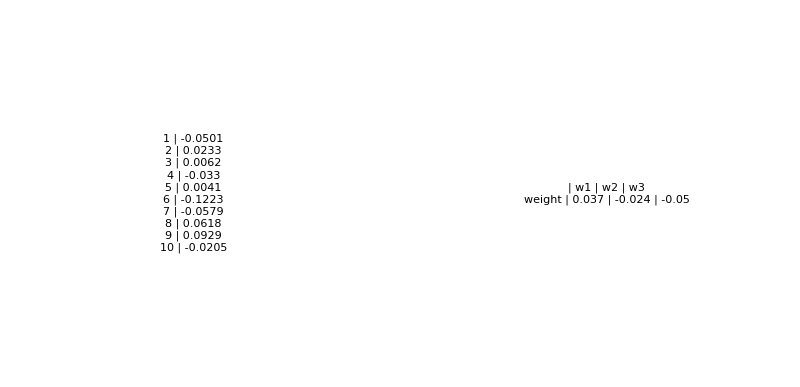

```mathematica
Show[GraphicsRow[{netTable,weightTable}]]
```

Table (Activation values Weights}

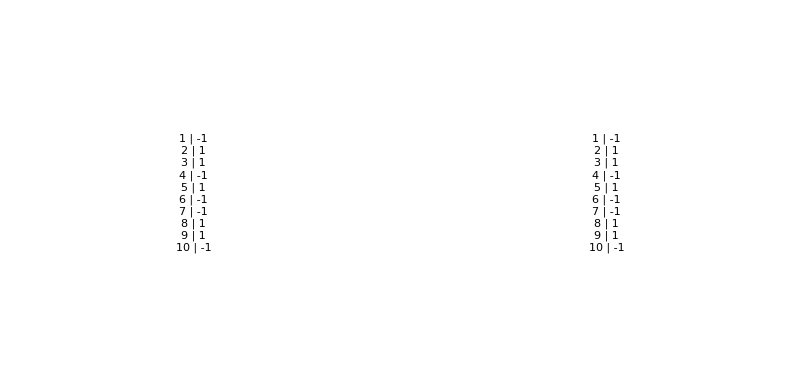

```mathematica
Show[GraphicsRow[{outputTable,desiredTable}]]
```

#### Show graphs

Error Graph

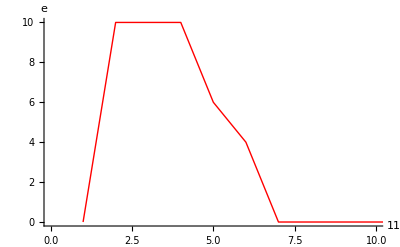

```mathematica
Show[errorGraph,DisplayFunction->$DisplayFunction]
```

Region Graph

```mathematica
Show[r1Graph,r2Graph,DisplayFunction->$DisplayFunction]
```

-Graphics-

The Seperation

```mathematica
Show[Vseperationgraph[[10]],DisplayFunction->$DisplayFunction]
```

-Graphics-

The progression of the seperation

```mathematica
Show[GraphicsGrid[{{Vseperationgraph⟦1⟧,Vseperationgraph⟦2⟧},{Vseperationgraph⟦3⟧,Vseperationgraph⟦4⟧},{Vseperationgraph⟦5⟧,Vseperationgraph⟦6⟧},{Vseperationgraph⟦7⟧,Vseperationgraph⟦8⟧},{Vseperationgraph⟦9⟧,Vseperationgraph⟦10⟧}}],DisplayFunction->$DisplayFunction]
```

-Graphics-